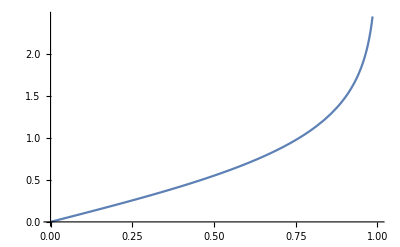

```mathematica
Plot[ArcTanh[x],{x,0,1}]
```

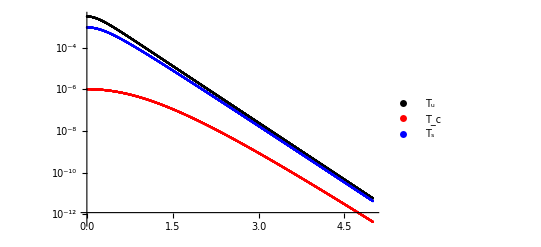

```mathematica
pt=Table[x,{x,0,5,0.001}];
mt=Sqrt[pt^2+1.5^2];
T=0.175;
vt=0.3;
Thermal=2*6*0.26*mt/(2Pi)^3 BesselI[0,pt*Sinh[ArcTanh[vt]]/T]*BesselK[1,mt*Cosh[ArcTanh[vt]]/T];
list=Table[{pt[[i]],Thermal[[i]]},{i,1,Length[pt]}];
c=ListLogPlot[list,PlotLegends->{"T_c"},PlotStyle->{Red}];

pt=Table[x,{x,0,5,0.001}];
mt=Sqrt[pt^2+0.26^2];
T=0.175;
vt=0.3;
Thermal=2*6*1*mt/(2Pi)^3 BesselI[0,pt*Sinh[ArcTanh[vt]]/T]*BesselK[1,mt*Cosh[ArcTanh[vt]]/T];
list=Table[{pt[[i]],Thermal[[i]]},{i,1,Length[pt]}];
u=ListLogPlot[list,PlotLegends->{"T_u"},PlotStyle->Black];

mt=Sqrt[pt^2+0.46^2];
T=0.175;
vt=0.3;
Thermal=2*6*0.8*mt/(2Pi)^3 BesselI[0,pt*Sinh[ArcTanh[vt]]/T]*BesselK[1,mt*Cosh[ArcTanh[vt]]/T];
list=Table[{pt[[i]],Thermal[[i]]},{i,1,Length[pt]}];
s=ListLogPlot[list,PlotLegends->{"T_s"},PlotStyle->Blue];

Show[{u,c,s},PlotRange->Automatic]
```

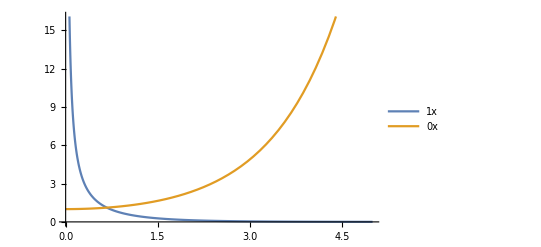

```mathematica
Plot[{BesselK[1,x],BesselI[0,x]},{x,0,5},PlotLegends->"Expressions"]
```

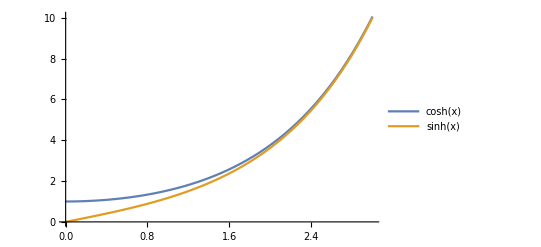

```mathematica
Plot[{Cosh[x],Sinh[x]},{x,0,3},PlotLegends->"Expressions"]
```